```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 1245 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[αReplace] (* Check this, is this true? Constants vs. time dependence *) 
αReplace = 
α -> θ + ψ
```

α→θ+ψ

```mathematica
Clear[r1]
r1 = 
{ - b Sin[ α + ϕ[t] ] , - b Cos[ α + ϕ[t] ] }
```

{-b Sin[α+ϕ[t]],-b Cos[α+ϕ[t]]}

```mathematica
D[r1, t]
```

{-b Cos[α+ϕ[t]] ϕ'[t],b Sin[α+ϕ[t]] ϕ'[t]}

```mathematica
D[r1, t] . D[r1, t]
```

b^2 Cos[α+ϕ[t]]^2 ϕ'[t]^2+b^2 Sin[α+ϕ[t]]^2 ϕ'[t]^2

```mathematica
D[r1, t] . D[r1, t]  // Expand
```

b^2 Cos[α+ϕ[t]]^2 ϕ'[t]^2+b^2 Sin[α+ϕ[t]]^2 ϕ'[t]^2

```mathematica
D[r1, t] . D[r1, t]  // Expand  // Simplify
```

b^2 ϕ'[t]^2

```mathematica
Clear[r2]
r2 = 
{ - b Sin[ α - ϕ[t] ] , - b Cos[ α - ϕ[t] ] }
```

{-b Sin[α-ϕ[t]],-b Cos[α-ϕ[t]]}

```mathematica
D[r2, t]
```

{b Cos[α-ϕ[t]] ϕ'[t],-b Sin[α-ϕ[t]] ϕ'[t]}

```mathematica
D[r2, t] . D[r2, t]
```

b^2 Cos[α-ϕ[t]]^2 ϕ'[t]^2+b^2 Sin[α-ϕ[t]]^2 ϕ'[t]^2

```mathematica
D[r2, t] . D[r2, t] // Expand
```

b^2 Cos[α-ϕ[t]]^2 ϕ'[t]^2+b^2 Sin[α-ϕ[t]]^2 ϕ'[t]^2

```mathematica
D[r2, t] . D[r2, t] // Expand  // Simplify
```

b^2 ϕ'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[r1, t] . D[r1, t]  // Expand  // Simplify  ) + 1/2 m ( D[r2, t] . D[r2, t] // Expand  // Simplify  )
```

b^2 m ϕ'[t]^2

```mathematica
r1
r1[[2]]
r2
r2[[2]]
```

{-b Sin[α+ϕ[t]],-b Cos[α+ϕ[t]]}

-b Cos[α+ϕ[t]]

{-b Sin[α-ϕ[t]],-b Cos[α-ϕ[t]]}

-b Cos[α-ϕ[t]]

```mathematica
Clear[V]
V = m g ( r1[[2]] ) + m g ( r2[[2]] )
```

-b g m Cos[α-ϕ[t]]-b g m Cos[α+ϕ[t]]

```mathematica
Clear[ℒ]
ℒ = T - V  ;
ℒ // pdConv
```

b^2 m ((∂ϕ(t))/(∂t))^2+b g m cos(α-ϕ(t))+b g m cos(α+ϕ(t))

```mathematica
Clear[q]
q = ϕ[t]
```

ϕ[t]

```mathematica
D[ D[ ℒ , D[q, t] ], t ]  - D[ ℒ , q ]
```

-b g m Sin[α-ϕ[t]]+b g m Sin[α+ϕ[t]]+2 b^2 m ϕ''[t]

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-2 b m (g Cos[α] Sin[ϕ[t]]+b ϕ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
m -> 0.5 , 
g -> 9.8 , 
b -> 0.3 , 
α -> π/12 + π/12
} ;
parameters // TableForm
```

m→0.5
g→9.8
b→0.3
α→π/6

```mathematica
eqs /. parameters  // Expand
```

-2.54611 Sin[ϕ[t]]-0.09 ϕ''[t]==0

```mathematica
Clear[ics]
ics = { 
ϕ[0] == π/20  , 
ϕ'[0] == 0 
} ;
ics // TableForm
```

ϕ[0]==π/20
ϕ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ { eqs }  /. parameters , ics ] , q , { t, 0, 300 } ]  ]
```

{ϕ[t]→InterpolatingFunction[…][t]}

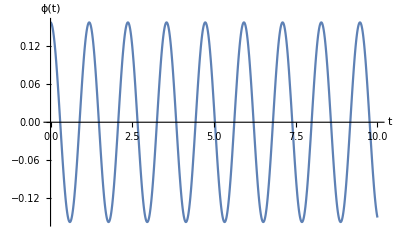

```mathematica
Plot[ q /. solution[t] , { t, 0, 10 } , AxesLabel->{ t , q } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q, D[q, t] } ]  ,
{ tmax , 1 ,20 , 0.5  } ]
```